# Analysis of Stopping Times for a 1D Random Walk with Absorption

## Milan Cvitkovic

## Section 01: Introduction

A random walk with absorption is one in which the walk ends when the walker’s position reaches a certain point, the analogy being that there are 1 or more barriers located in the random walk space which will absorb the random walker if he reaches it/them.  In this notebook, we will be exploring the case in which a random walker, with equal probability of going left or right at a given step, starts at the origin and walks along a number line containing two absorption barriers, one some distance a to the left of the origin (a<0) and one some distance b to the right of the origin (b>0).  We will first examine what the probability distribution looks like for a specific a and b value and draw conclusions about this scenario from that.  Then we will derive a formula with which we can relate the average stopping time of the random walk to a and b.

## Section 02: Needed Packages

```mathematica
Needs["ErrorBarPlots`"]
```

## Section 03: Statistical Functions

Creating a function Ave[List] with which to find the arithmetic mean of an inputted list:

```mathematica
Clear[Ave]
Ave[List_] := Apply[Plus,List]/Length[List]
```

Testing:

```mathematica
Clear[TestList]
TestList = {a,b,c,d}
Ave[TestList]
```

{a,b,c,d}

1/4 (a+b+c+d)

## Section 04: Setting Up Code to Simulate a Random Walk with Absorption

We will first create a function nextStep[] to randomly generate a next step for our random walker:

```mathematica
Clear[nextStep]
nextStep := 2*RandomInteger[{0,1}]-1
```

Testing:

```mathematica
Table[nextStep, {10}]
```

{-1,-1,1,-1,-1,1,1,-1,-1,1}

Next we will create a module walkTime[a,b] which will simulate a random walk with absorption, stop when the random walker reaches barrier a or b, and output the number of steps taken:

```mathematica
Clear[walkTime]
walkTime[a_,b_] :=
Module[{xPosition,t},

xPosition= 0; t = 0;
While[a<xPosition <b,
(
xPosition+=nextStep;
t++;
)];
t
]
```

Testing:

```mathematica
Table[walkTime[-1,1],{10}]
```

{1,1,1,1,1,1,1,1,1,1}

```mathematica
Table[walkTime[-1,2],{10}]
```

{2,1,2,2,1,2,2,1,1,1}

```mathematica
Table[walkTime[-5,10],{10}]
```

{7,24,73,33,13,54,94,15,19,19}

## Section 05: Probability Distribution for a Specific a and b

Using the function walkTime[a,b] created above, we will now simulate a large number of random walks for the specific case of a = -5 and b = 10 and plot the results to get a rough sense of the probability distribution of stopping times:

Finding the stopping times from 100000 simulated random walks:

```mathematica
Clear[probDistData]
probDistData = Table[walkTime[-5,10],{100000}]
```

{17,21,68,45,54,80,13,62,11,201,35,175,48,39,33,11,38,49,150,53,86,53,56,99,64,19,48,13,28,61,41,95,34,54,160,15,50,92,22,15,33,46,11,31,49,62,60,17,187,80,17,13,68,61,30,7,145,225,37,96,29,55,29,28,15,88,35,5,87,21,«99860»,23,39,9,128,46,158,97,5,17,27,52,28,32,19,169,90,43,5,34,31,27,21,9,19,119,9,15,15,5,150,5,124,37,33,42,11,70,9,42,15,45,11,28,15,44,76,21,18,11,51,24,49,21,9,29,43,13,11,40,5,11,12,13,83,79,43,208,59,105,33}

Plotting a Histogram showing the number of occurences of each stopping time:

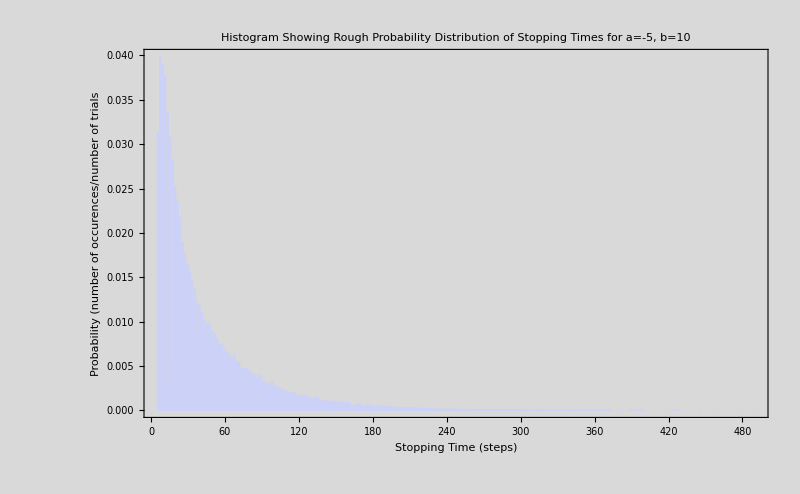

```mathematica
Clear[Plot01]
Plot01 = Histogram[probDistData,{1},"Probability", Frame->True, PlotLabel -> "Histogram Showing Rough Probability Distribution of Stopping Times for a=-5, b=10", FrameLabel -> {"Stopping Time (steps)", "Probability (number of occurences/number of trials"}, GridLines -> Automatic,Background -> LightGray, ImageSize -> 800]
```

This rough probability distribution indicates that the most likely stopping times of a walk is 7 steps, with a minumim length of 5 (unsurprisingly, since our nearest absorption barrier was 5 spaces away from the origin).  This distribution also shows us that odd-length walks are, for short stopping times, far more likely than even length walks, but that this gap in probability diminishes as stopping time increases.  Specifically, odd-length walks are vastly more likely in the beginning and then, after quickly peaking at 7, gradually decrease as stopping time increases, whereas even-length walks are much less likely early on, but then peak at around 30 and eventually become of similar likelyhood to odd length walks as they both gradually decrease in likelyhood.  This is understandable since the barrier nearer to the origin is an odd number of spaces (5) away and the far barrier is an even number of spaces (10) away.  Thus it is more likely in a short timespan that a walk will hit the near barrier than the far barrier (in fact for walks fewer than 10 steps long it is a 100% chance that it will hit the near barrier), and hence we see this uneven probability distribution.

## Section 06: Stopping Times for Arbitrary Values of a and b

Now we will examine how the average stopping time of a walk changes for various values of a and b.

First we will define a function aveWalkTime[a,b,numTrials] which will return the average stopping time (in numerical format) of a random walk with absorption barriers at a and b (a<0, b>0) for numTrials number of random walks:

```mathematica
Clear[aveWalkTime]
aveWalkTime[a_,b_,numTrials_] := N[Ave[Table[walkTime[a,b],{numTrials}]]]
```

Testing:

```mathematica
aveWalkTime[-1,1,10000]
aveWalkTime[-1,10,10000]
aveWalkTime[-5,10,10000]
```

1.

10.0252

50.0943

Now we will look at how changes in the position of barrier a affect the average stopping time of a random walk assuming a constant value for b:

Creating a module varAveWalkTime[aStart,aEnd,b,numTrials] which will, for each value of a from aStart to aEnd, run numTrials random walks with absorption barriers at a and b (a<0, b>0) and return a list containing the average stopping time of the walk for all the values of a tried in the form {a,average stopping time}:

```mathematica
Clear[varAveWalkTime]
varAveWalkTime[aStart_,aEnd_,b_,numTrials_] :=
Module[
{outputList, aCurrent},

aCurrent = aStart; outputList = {};
While[(aCurrent>aEnd),
(
outputList = Append[outputList,{aCurrent,aveWalkTime[aCurrent,b,numTrials]}];
aCurrent -= 1;)];

outputList
]
```

Testing:

```mathematica
varAveWalkTime[-1,-10,10,100]
varAveWalkTime[-1,-20,10,100]
varAveWalkTime[-1,-10,20,100]
```

{{-1,8.18},{-2,17.12},{-3,28.32},{-4,39.12},{-5,44.85},{-6,67.76},{-7,66.57},{-8,83.14},{-9,86.49}}

{{-1,8.91},{-2,14.82},{-3,27.11},{-4,44.44},{-5,50.43},{-6,58.2},{-7,73.69},{-8,79.98},{-9,99.3},{-10,115.84},{-11,97.4},{-12,141.78},{-13,126.45},{-14,148.24},{-15,157.47},{-16,164.02},{-17,165.72},{-18,181.72},{-19,199.72}}

{{-1,19.33},{-2,37.02},{-3,73.13},{-4,72.9},{-5,101.37},{-6,108.98},{-7,156.52},{-8,159.08},{-9,159.3}}

Let’s look at what happens when we plot the average length of walk for varying positions of a from -1 to -10 with b at 10 and 10000 trials for each random walk:

```mathematica
data01 = varAveWalkTime[-1,-10,10,10000]
```

{{-1,10.3735},{-2,19.7088},{-3,29.5794},{-4,40.2346},{-5,50.0223},{-6,60.0082},{-7,70.2055},{-8,79.826},{-9,89.4831}}

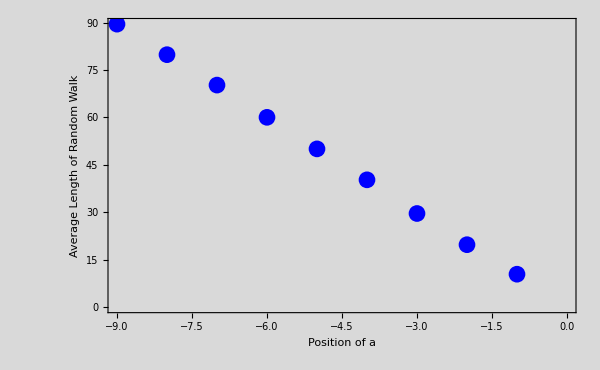

```mathematica
Plot02 = ListPlot[data01, Frame -> True, ImageSize -> 600, Background -> LightGray, PlotStyle -> {RGBColor[0,0,1],PointSize[0.02]},FrameLabel -> {"Position of a","Average Length of Random Walk","Position of Barrier a with Barrier b at 10"}, GridLines -> Automatic]
```

We see here what appears to be a linear relationship between the distance of a from the origin and the average length of a random walk.  We can find a linear fit for these data using the LinearModelFit[] function:

```mathematica
Clear[x]
bestFit = LinearModelFit[data01,{1,x},x]
```

FittedModel[0.11995-9.9636 x]

Calculating standard errors for these values:

```mathematica
bestFit["ParameterErrors"]
```

{0.226814,0.0403058}